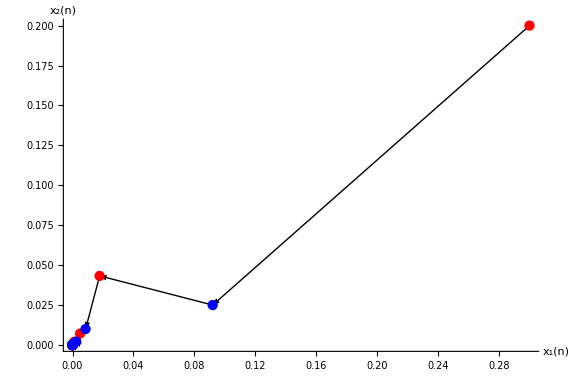

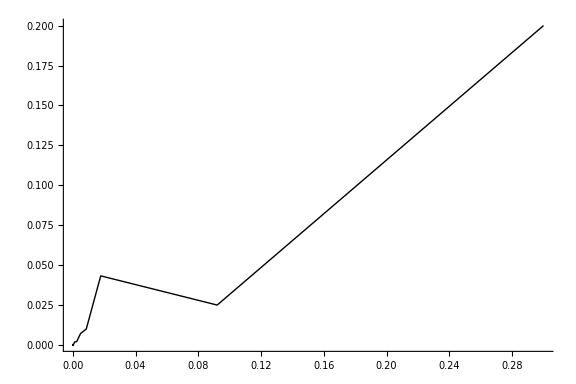

η_2=0.9706

η_1=0.154

D:\LaTeX\Изчислителна\migrationSimulation4.jpg

-Graphics-

η_2=0.9706

η_1=0.154

D:\LaTeX\Изчислителна\migrationSimulation4.jpg

-Graphics-

η_2=0.9706

η_1=0.154

η_1=12.75`

η_2=1.

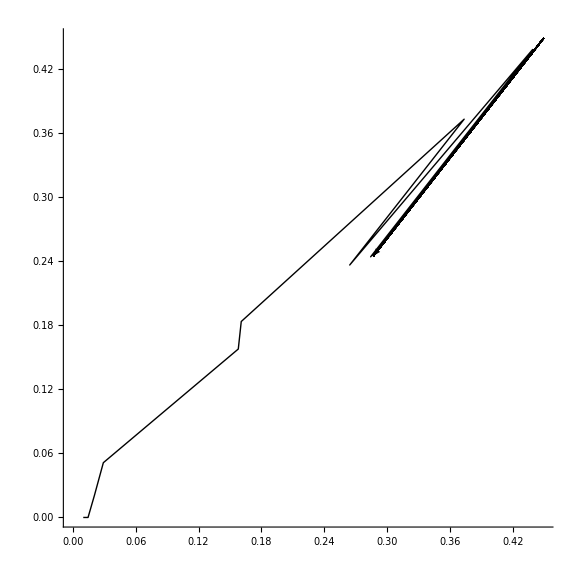

D:\LaTeX\Изчислителна\migrationSimulation3.jpg

```mathematica
(*Параметри*)
Subscript[α, 1]=0.7;
Subscript[α, 2]=0.7;
Subscript[β, 1]=4;
Subscript[β, 2]=10;
Subscript[a, 1]=0.5;
Subscript[a, 2]=0.3;
Subscript[b, 1]=2.1;
Subscript[b, 2]=7;
Subscript[d, 1]=0.8;
Subscript[d, 2]=0.6;
Subscript[η, 1]=Subscript[a, 1] Subscript[α, 1] (1-Subscript[d, 1]) + Subscript[a, 2] Subscript[α, 2] (1-Subscript[d, 2]);
eta1str=StringForm["η_1=``",Subscript[η, 1]]
Subscript[η, 2]=1+Subscript[a, 1] Subscript[a, 2] Subscript[α, 1] Subscript[α, 2] (1-Subscript[d, 1] -Subscript[d, 2]);
eta2str=StringForm["η_2=``",Subscript[η, 2]]
x10=0.3;
x20=0.2;
T=50;
x=Table[Table[0,T+1],2];
x[[1]][[1]]=x10;
x[[2]][[1]]=x20;
(*x[[1]][[2]]=x[[1]][[1]] Subscript[a, 1]/(1+Subscript[b, 1] x[[1]][[1]])
x[[2]][[2]]=x[[2]][[1]] Subscript[a, 1]/(1+Subscript[b, 1] x[[2]][[1]])
x[[1]][[3]]=(1-Subscript[d, 1]) x[[1]][[2]] Subscript[α, 1]/(1+Subscript[β, 1] x[[1]][[2]])+ Subscript[d, 2] x[[2]][[2]] Subscript[α, 2]/(1+Subscript[β, 2] x[[2]][[2]])
x[[2]][[3]]=Subscript[d, 1] x[[1]][[2]] Subscript[α, 1]/(1+Subscript[β, 1] x[[1]][[2]])+ (1-Subscript[d, 2]) x[[2]][[2]] Subscript[α, 2]/(1+Subscript[β, 2] x[[2]][[2]])
x*)
(*Симулация*)
(*При нас k=n+1, заради началото на списъците*)
For[k=1,k<=T,k++,
If[Mod[k-1,2]==0,
(*n - четно*)
x[[1]][[k+1]]=x[[1]][[k]] Subscript[a, 1]/(1+Subscript[b, 1] x[[1]][[k]]);
x[[2]][[k+1]]=x[[2]][[k]] Subscript[a, 2]/(1+Subscript[b, 2] x[[2]][[k]]);,
(*n - нечетно*)
x[[1]][[k+1]]=(1-Subscript[d, 1]) x[[1]][[k]] Subscript[α, 1]/(1+Subscript[β, 1] x[[1]][[k]])+ Subscript[d, 2] x[[2]][[k]] Subscript[α, 2]/(1+Subscript[β, 2] x[[2]][[k]]);
x[[2]][[k+1]]=Subscript[d, 1] x[[1]][[k]] Subscript[α, 1]/(1+Subscript[β, 1] x[[1]][[k]])+ (1-Subscript[d, 2]) x[[2]][[k]] Subscript[α, 2]/(1+Subscript[β, 2] x[[2]][[k]]);
];
];

(*Графично представяне*)
Animate[
ListPlot[{{x[[1]][[n]],x[[2]][[n]]}},PlotStyle->If[Mod[n,2]==1,Red,Blue],ImageSize->Large,PlotRange->{{0,Max[x[[1]]]},{0,Max[x[[2]]]}}],
{n,1,T+1,1},AnimationRunning->False,DefaultDuration->5,DisplayAllSteps->True]
Manipulate[
ListPlot[{{x[[1]][[n]],x[[2]][[n]]}},PlotStyle->If[Mod[n,2]==1,Red,Blue],ImageSize->Large,PlotRange->{{0,Max[x[[1]]]},{0,Max[x[[2]]]}}],
{n,1,T+1,1}]
Manipulate[
Graphics[Arrow[{{x[[1]][[n]],x[[2]][[n]]},{x[[1]][[n+1]],x[[2]][[n+1]]}}],ImageSize->Large,PlotRange->{{0,Max[x[[1]]]},{0,Max[x[[2]]]}},Axes->True],
{n,1,T,1}]
Graphics[Arrow[Table[{x[[1]][[n]],x[[2]][[n]]},{n,1,T}]],ImageSize->Large,PlotRange->{{0,Max[x[[1]]]},{0,Max[x[[2]]]}},Axes->True]
arrows=Graphics[Table[Arrow[{{x[[1]][[n]],x[[2]][[n]]},{x[[1]][[n+1]],x[[2]][[n+1]]}}],{n,1,T}],ImageSize->Large,PlotRange->{{0,Max[x[[1]]]},{0,Max[x[[2]]]}},Axes->True, AxesLabel->{Style["x_1(n)",FontSize->14],Style["x_2(n)",FontSize->14]}(*,
PlotLabel->Style[ToString[eta1str] <>", " <> ToString[eta2str],FontSize->12]*)];
evens=ListPlot[Table[{x[[1]][[n]],x[[2]][[n]]},{n,1,T,2}],PlotStyle->Red,ImageSize->Large,PlotRange->{{0,Max[x[[1]]]},{0,Max[x[[2]]]}}];
odds=ListPlot[Table[{x[[1]][[n]],x[[2]][[n]]},{n,2,T,2}],PlotStyle->Blue,ImageSize->Large,PlotRange->{{0,Max[x[[1]]]},{0,Max[x[[2]]]}}];

Show[arrows,evens,odds]
(*Export["D:\\LaTeX\\Изчислителна\\migrationSimulation4.jpg",Show[arrows,evens,odds]]*)
```